#### 热学第六次作业

#### (1).

B_2=(- N_A)/2∫ f (r⃗)d r⃗
      =  2π N_A(∫_0^σ r^2 ⅆr-∫_σ^σ' r^2(e^(-β u_0)-1)ⅆr)
      = 2π N_A (1/3 σ^3 + ∫_σ^σ' r^2(e^(-β u_0)-1)ⅆr)
      = 2π N_A  (1/3 σ^3+ 1/3 e^(-β u_0)(σ'^3-σ^3)-1/3(σ'^3-σ^3))
      ≈ 2π N_A (1/3 σ^3+ 1/3(1-β u_0)(σ'^3-σ^3)-1/3(σ'^3-σ^3))
      = 2π N_A (1/3 σ^3-β u_0(σ'^3-σ^3))
      → b-a/(R T)

P V=N k_B T(1+(n B_2)/V)
         = N k_B(T+(n b)/V)-(n^2 a)/V
         ≈(N k_B T)/(1-(n b)/V)-(n^2 a)/V
→ (p + (a n^2)/V^2)(V-n b) = n R T

#### (2).

```mathematica
d=(2η(η^2-3η-3+Sqrt[3(η^4-2 η^3+η^2+6η+3)]))^(1/3);
μ=(2η)/(1-η)(-1-d/(2η)-η/d)/σ;
Subscript[α, 0]=(2η)/(1-η)(-1+d/(4η)-η/(2d));
Subscript[β, 0]=(2η)/(1-η)Sqrt[3](-d/(4η)-η/(2d));
γ=ArcTan[-σ/Subscript[β, 0](Subscript[α, 0]*σ(Subscript[α, 0]^2+Subscript[β, 0]^2)-μ*σ(Subscript[α, 0]^2+Subscript[β, 0]^2)*(1+1/2 η)+(Subscript[α, 0]^2+Subscript[β, 0]^2-μ*Subscript[α, 0])(1+2η))];
ω=(-0.682Exp[-24.697η]+4.720+4.450η)/σ;
κ=(4.674Exp[-3.935η]+3.536Exp[-56.270η])/σ;
α=(44.554+79.868η+116.432 η^2-44.652Exp[2η])/σ;
β=(-5.022+5.857η+5.089Exp[-4η])/σ;
SuperStar[r]=(2.0116-1.0647η+0.0538 η^2)σ;
Subscript[g, m]=1.0286-0.6095η+3.5781 η^2-21.3651 η^3+42.6344 η^4-33.8485 η^5;
Subscript[g, σ]=1/(4η)((1+η+η^2-2/3 η^3-2/3 η^4)/(1-η)^3-1);

B=(Subscript[g, m]-(σ*Subscript[g, σ]/SuperStar[r])Exp[μ(SuperStar[r]-σ)])/(Cos[β(SuperStar[r]-σ)+γ]Exp[α(SuperStar[r]-σ)]-Cos[γ]Exp[μ(SuperStar[r]-σ)])SuperStar[r];
A=σ*Subscript[g, σ]-B*Cos[γ];
δ=-ω*SuperStar[r]-ArcTan[(κ*SuperStar[r]+1)/(ω*SuperStar[r])];
c=(SuperStar[r](Subscript[g, m]-1)Exp[κ*SuperStar[r]])/Cos[ω*SuperStar[r]+δ];
g1[r_]:=0;
g2[r_]:=A/r Exp[μ(r-σ)]+B/r Cos[β(r-σ)+γ]Exp[α(r-σ)];
g3[r_]:=1+c/r Cos[ω*r+δ]Exp[-κ*r];
```

```mathematica
g2[r]/.η->{0.15,0.20,0.25,0.30}
g3[r]/.η->{0.15,0.20,0.25,0.30}
```

{1/r e^(-(1.89067 (r-σ))/σ) (1.50835 σ-(1.48687 σ)/(√(1+0.563869 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ)^2 σ^2) (-0.1993/(√(1+0.563869 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ)^2 σ^2))+0.384636 Cos[1.15216-ArcTan[0.750912 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ) σ]])))+(1.48687 ⅇ^(-(1.11998 (r-σ))/σ) σ Cos[(1.35055 (r-σ))/σ-ArcTan[0.750912 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ) σ]])/(r (-0.1993/(√(1+0.563869 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ)^2 σ^2))+0.384636 Cos[1.15216-ArcTan[0.750912 (5.97595+1.3 (2.94024-2.04226/σ)-3.17597 σ) σ]])),1/r e^(-(2.34242 (r-σ))/σ) (1.76172 σ-(1.41613 σ)/(√(1+0.392791 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ)^2 σ^2) (-0.153227/(√(1+0.392791 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ)^2 σ^2))+0.318663 Cos[1.25244-ArcTan[0.626731 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ) σ]])))+(1.41613 ⅇ^(-(1.42808 (r-σ))/σ) σ Cos[(1.56396 (r-σ))/σ-ArcTan[0.626731 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ) σ]])/(r (-0.153227/(√(1+0.392791 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ)^2 σ^2))+0.318663 Cos[1.25244-ArcTan[0.626731 (11.2605+1.4 (4.37017-3.16382/σ)-5.90263 σ) σ]])),1/r e^(-(2.83455 (r-σ))/σ) (2.08025 σ-(1.32398 σ)/(√(1+0.283704 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ)^2 σ^2) (-0.119734/(√(1+0.283704 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ)^2 σ^2))+0.25581 Cos[1.26216-ArcTan[0.532638 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ) σ]])))+(1.32398 ⅇ^(-(1.8207 (r-σ))/σ) σ Cos[(1.68561 (r-σ))/σ-ArcTan[0.532638 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ) σ]])/(r (-0.119734/(√(1+0.283704 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ)^2 σ^2))+0.25581 Cos[1.26216-ArcTan[0.532638 (19.8456+1.5 (6.22339-4.65643/σ)-10.2234 σ) σ]])),1/r e^(-(3.38331 (r-σ))/σ) (2.48688 σ-(1.21406 σ)/(√(1+0.208936 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ)^2 σ^2) (-0.0945831/(√(1+0.208936 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ)^2 σ^2))+0.191944 Cos[1.20734-ArcTan[0.457096 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ) σ]])))+(1.21406 ⅇ^(-(2.36797 (r-σ))/σ) σ Cos[(1.73212 (r-σ))/σ-ArcTan[0.457096 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ) σ]])/(r (-0.0945831/(√(1+0.208936 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ)^2 σ^2))+0.191944 Cos[1.20734-ArcTan[0.457096 (33.65+1.6 (8.64859-6.64926/σ)-16.9972 σ) σ]]))}

{1+(C ⅇ^(-(2.59104 r)/σ) Cos[10.4803-(5.37072 r)/σ])/r,1+(C ⅇ^(-(2.12769 r)/σ) Cos[10.5402-(5.60512 r)/σ])/r,1+(C ⅇ^(-(1.74764 r)/σ) Cos[10.5759-(5.83108 r)/σ])/r,1+(C ⅇ^(-(1.4355 r)/σ) Cos[10.5976-(6.05459 r)/σ])/r}

```mathematica
g2[r]/.{η->{0.15,0.20,0.25,0.30},σ->1}
g3[r]/.{η->{0.15,0.20,0.25,0.30},σ->1}
```

{(0.0273842 ⅇ^(-1.89067 (-1+r)))/r+(4.65391 ⅇ^(-1.11998 (-1+r)) Cos[1.24695-1.35055 (-1+r)])/r,(0.658073 ⅇ^(-2.34242 (-1+r)))/r+(4.99752 ⅇ^(-1.42808 (-1+r)) Cos[1.34812-1.56396 (-1+r)])/r,(1.20473 ⅇ^(-2.83455 (-1+r)))/r+(5.65151 ⅇ^(-1.8207 (-1+r)) Cos[1.41525-1.68561 (-1+r)])/r,(1.72885 ⅇ^(-3.38331 (-1+r)))/r+(6.9201 ⅇ^(-2.36797 (-1+r)) Cos[1.46104-1.73212 (-1+r)])/r}

{1-(0.0759565 ⅇ^(4.80147-2.59104 r) Cos[10.4803-5.37072 r])/r,1-(0.127203 ⅇ^(3.83157-2.12769 r) Cos[10.5402-5.60512 r])/r,1-(0.189125 ⅇ^(3.05625-1.74764 r) Cos[10.5759-5.83108 r])/r,1-(0.26124 ⅇ^(2.43609-1.4355 r) Cos[10.5976-6.05459 r])/r}

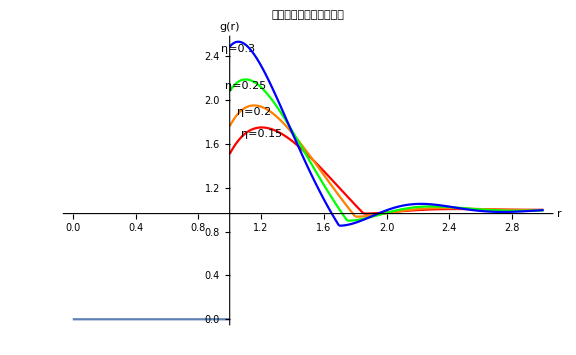

```mathematica
Show@@Flatten@{ReleaseHold[Hold[Plot[g2[r]/.{η->#,σ->1},{r,1,(2.0116-1.0647η+0.0538 η^2)σ/.{η->#,σ->1}},PlotRange->All,PlotStyle->#2,PlotLabels->Placed[StringJoin["η=",ToString[#1]],Top],AxesLabel->{Style["r",Black],Style["g(r)",Black]}]]&@@@{{0.15,Red},{0.20,Orange},{0.25,Green},{0.30,Blue}}],ReleaseHold[Hold[Plot[g3[r]/.{η->#,σ->1},{r,(2.0116-1.0647η+0.0538 η^2)σ/.{η->#,σ->1},3},PlotStyle->#2,PlotRange->All]]&@@@{{0.15,Red},{0.20,Orange},{0.25,Green},{0.30,Blue}}],Plot[0,{x,0,1}],ImageSize->Large,PlotLabel->Style["硬球模型模型分布函数图",18,Black]}
```

#### (3).

首先，相变意味着至少一个物理量发生了非连续的改变——这是由于如果所有物理量都是连续性的改变，我们将无法具有能够区分这两个相的一个标准。我们将“肉眼可见”的相变定义为一级相变，因为这是最直观的，是我们最先能够发现的一个现象，比如体积的增大，而这在Ehrenfest中定义为自由能的一阶导的不连续性——因为自由能的一阶导包含了体积一项。而更高级的相变则是“不直观”的相变，需要通过间接的手段来测量，在Ehrenfest理论中，二级相变就被定义为自由能二阶导的不连续性。因此如液体的沸腾，固体的熔化都属于一级相变，而顺磁与铁磁之间的转化，介电性质的非连续性改变等都是二级相变。

朗道理论用统计的角度指出了二级相变的意义；他通过引入序参量来描述由于微观上的变化引起的宏观物理量的变化。一级相变需要跨越能垒，而二级相变并不需要跨越这样的能垒，是在环境（特别是温度）的改变下某个相变为不稳定相，从而转变成其他相。

#### (4).

(a).

```mathematica
F[n_,x_]:=Subscript[F, 0]+n x^2+Subscript[a, 3] x^3+Subscript[a, 4] x^4;
```

```mathematica
Solve[D[F[n,x],x]==0,x]
```

{{x→0},{x→(-3 a_3-√(9 a_3^2-32 n a_4))/(8 a_4)},{x→(-3 a_3+√(9 a_3^2-32 n a_4))/(8 a_4)}}

发生crossover时，满足9 a_3^2-32 n a_4=0,
即n=(9 a_3^2)/(32 a_4),或a_2^*=(9 a_3^2)/(32 a_4).

(b).

```mathematica
Reduce[F[n,0]>F[n,(-3 Subscript[a, 3]+√(9 Subscript[a, 3]^2-32 n Subscript[a, 4]))/(8 Subscript[a, 4])],n]
```

F_0∈Reals&&((a_3≤0&&((a_4<0&&(9 a_3^2)/(32 a_4)≤n<a_3^2/(4 a_4))||(a_4>0&&n<a_3^2/(4 a_4))))||(a_3>0&&((a_4<0&&(9 a_3^2)/(32 a_4)≤n<0)||(a_4>0&&n<0))))

故a_(2,p)=a_2^*=(9 a_3^2)/(32 a_4).

(c).

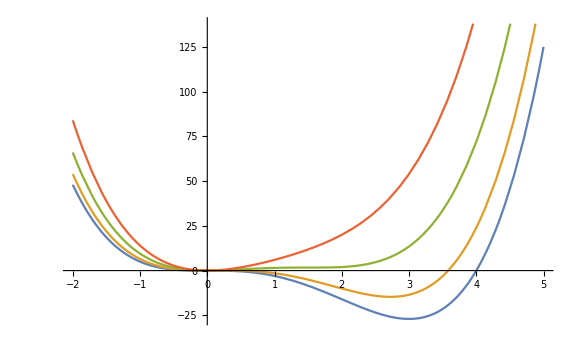

```mathematica
Plot[Evaluate[(F[#,x]&/@((9 Subscript[a, 3]^2)/(32 Subscript[a, 4])*{0,1/3,1,2}))/.{Subscript[a, 3]->-4,Subscript[a, 4]->1,Subscript[F, 0]->0}],{x,-2,5},ImageSize->Large]
```

#### (5).

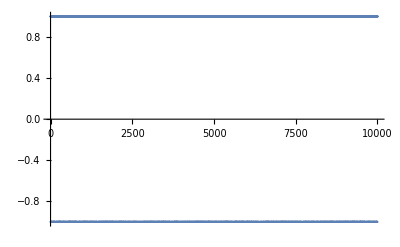

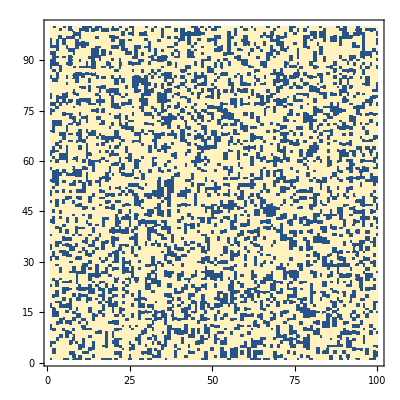

```mathematica
Ising[length_,weight_List]:=Table[{i,RandomChoice[weight->{-1,1}]},{i,length}];
Ising2D[length_,weight_List]:=Flatten[Table[{i,j,RandomChoice[weight->{-1,1}]},{i,length},{j,length}],1];
(*
这里面的weight表示朝上与朝下（在这里面是-1与1）的概率比。若想要朝下与朝上的概率比是1:2，则在相对应位置输入{1,2}。
*)
ListPlot[Evaluate[Ising[10000,{1,2}]]]
ListDensityPlot[Ising2D[100,{1,2}],InterpolationOrder->0]
```

#### (6).

平均场在处理气体、液体等流体能够成功便是由于它们的各向同性，或者具体地来说在以参考微粒为中心的球面上的概率分布函数非常接近一个常数，即出现概率与方位无关。由于大量分子的存在以及各向同性，在球面上的分子与中心分子之间的力会被平均下来，从而可以近似成至于球面半径有关的函数，即“平均场”。用化学的角度更为深入地探讨的话，这是分子间作用力的无方向性、不饱和性、作用力较小等特性共同促进了平均场的成功。

Z=1/(N!h^(3N))∫e^-βU dΓ
  ≈ 1/(N!h^(3N))(∫∫∫∫e^(-β((p_x^2+p_y^2+p_z^2)/(2m)+ϕ(r⃗)))dp_x dp_y dp_z d r⃗)^N
  = 1/(N!h^(3N))(4π∫∫∫∫r^2 e^(-β((p_x^2+p_y^2+p_z^2)/(2m)+ϕ(r^)))dp_x dp_y dp_z d r^)^N
  = 1/(N! h^(3M))(4π((2π m)/β)^(3/2)∫r^2 e^(-ϕ(r^))dr)^N
  ≈1/(N!)((2π m)/(β h^2))^((3N)/2)(4π∫r^2(1-ϕ(r^))dr)^N
  = 1/(N!)((2π m)/(β h^2))^((3N)/2)(V-4π∫r^2 ϕ(r^)dr)^N
ln Z=ln 1/(N!)((2π m)/(β h^2))^((3N)/2)+N ln (V-4π∫r^2 ϕ(r^)dr)
(∂ ln Z)/(∂ V)=N/(V-4π∫r^2 ϕ(r^)dr)(1-(∂(4π∫r^2 ϕ(r^)dr))/(∂V))
	   =N/(V-4π∫r^2 ϕ(r^)dr)-N/(V-4π∫r^2 ϕ(r^)dr)(∂(4π∫r^2 ϕ(r^)dr))/(∂V)
	   ≈N/(V-n b)-(a n^2)/V^2
	   
→(p+(a n^2)/V^2)(V-nb)=N k_B T